```mathematica
Now
```

Wed 1 Jun 2016 09:31:43GMT-5.

```mathematica
$DateStringFormat
```

{DateTimeShort}

```mathematica
$DateStringFormat = {"Year", "Month", "Day", "_", "Hour", "Minute", "Second"}
```

{Year,Month,Day,_,Hour,Minute,Second}

```mathematica
Block[{$DateStringFormat={"Year", "Month", "Day", "_", "Hour", "Minute", "Second"}},DateString[]]
```

20160601_093417

```mathematica
Now
```

20160601_093343GMT-5.

```mathematica
csvFileName = "/scratch/gabella/Documents/astro/exop/exop_20160601_094040.csv"
```

/scratch/gabella/Documents/astro/exop/exop_20160601_094040.csv

```mathematica
Split[csvFileName]
```

Split::normal: Nonatomic expression expected at position 1 in Split[/scratch/gabella/Documents/astro/exop/exop_20160601_094040.csv].

```mathematica
cc=StringSplit["/scratch/gabella/Documents/astro/exop/exop_20160601_094040.csv", {"/"}]
```

{scratch,gabella,Documents,astro,exop,exop_20160601_094040.csv}

```mathematica
dd=StringSplit[cc[[-1]],"."]
```

{exop_20160601_094040,csv}

```mathematica
ee=StringSplit[dd[[1]],"_"]
```

{exop,20160601,094040}

```mathematica
ee[[2]]<>"_"<>ee[[3]]
```

20160601_094040

```mathematica
aa= ToExpression["ajunk"]
```

ajunk

```mathematica
aa=12
```

12

```mathematica
ajunk
```

ajunk

```mathematica
ajunk+2
```

2+ajunk

```mathematica
Evaluate[ToExpression["ajunk"]]=12
```

12

```mathematica
ajunk
```

12

```mathematica
ajunk+1
```

13

```mathematica
ajunk
```

ajunk

```mathematica
alist={"zz", "yy", "xx"}
```

{zz,yy,xx}

```mathematica
data = {{1,2,3},{4,5,6},{7,8,9}}
```

{{1,2,3},{4,5,6},{7,8,9}}

```mathematica
data//TableForm
```

1 | 2 | 3
4 | 5 | 6
7 | 8 | 9

```mathematica
Evaluate[ToExpression/@alist]=data
```

{{1,2,3},{4,5,6},{7,8,9}}

```mathematica
zz
```

```mathematica
zz
```

{1,2,3}

```mathematica
yy
```

{4,5,6}

```mathematica
xx
```

{7,8,9}

```mathematica
Evaluate[ToExpression/@alist]=Transpose[data]
```

Set::setraw: Cannot assign to raw object 1.

Set::setraw: Cannot assign to raw object 2.

Set::setraw: Cannot assign to raw object 3.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

{{1,4,7},{2,5,8},{3,6,9}}

```mathematica
xx
```

{7,8,9}

```mathematica
aa={List[one], List[two], List[three]}
```

{{{1,2,3}},{{4,5,6}},{{7,8,9}}}

```mathematica
Head/@{aa, aa[[2]]}
```

{List,List}

```mathematica
e
```

```mathematica
aa=data
```

{{1,2,3},{4,5,6},{7,8,9}}

```mathematica
one
```

one

```mathematica
{one, two, three} = data
```

{{1,2,3},{4,5,6},{7,8,9}}

```mathematica
one
```

{1,2,3}

```mathematica
Head[one]
```

List

```mathematica
Evaluate[aa]
```

{{{1,2,3}},{{4,5,6}},{{7,8,9}}}

```mathematica
aa
```

{{{1,2,3}},{{4,5,6}},{{7,8,9}}}

```mathematica
??PolarPlot
```

PolarPlot[r,{θ,θ_min,θ_max}] generates a polar plot of a curve with radius r as a function of angle θ.
PolarPlot[{f_1,f_2,…},{θ,θ_min,θ_max}] makes a polar plot of curves with radius functions f_1, f_2, ….

Attributes[PolarPlot]={HoldAll,Protected,ReadProtected}
 
Options[PolarPlot]:={AlignmentPoint→Center,AspectRatio→Automatic,Axes→Automatic,AxesLabel→None,AxesOrigin→{0,0},AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},EvaluationMonitor→None,Exclusions→Automatic,ExclusionsStyle→None,FormatType:>TraditionalForm,Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelStyle→{},MaxRecursion→Automatic,Mesh→None,MeshFunctions→{#3&},MeshShading→None,MeshStyle→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotLegends→None,PlotPoints→Automatic,PlotRange→Automatic,PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotStyle→Automatic,PlotTheme:>$PlotTheme,PolarAxes→False,PolarAxesOrigin→Automatic,PolarGridLines→None,PolarTicks→Automatic,PreserveImageOptions→Automatic,Prolog→{},RegionFunction→(True&),RotateLabel→True,Ticks→Automatic,TicksStyle→{},WorkingPrecision→MachinePrecision}

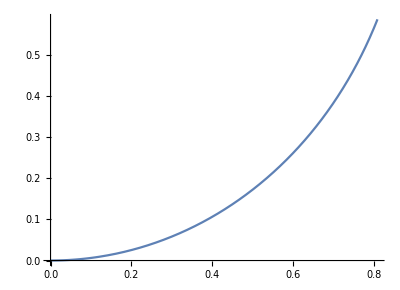

```mathematica
PolarPlot[ θ/(Pi/5),{θ,0,Pi/5}]
```

```mathematica
(*http://stackoverflow.com/questions/6187385/create-variable-with-list-of-strings*)
Remove[cow,monkey];
str={"cow","monkey"}
str
Head /@ str
str1=ToExpression/@str
Head /@ str1

{cow,monkey}
cow=12
str1[[1]]
```

{cow,monkey}

{cow,monkey}

{String,String}

{cow,monkey}

{Symbol,Symbol}

{cow,monkey}

12

12

```mathematica
?cow
?monkey
```

Global`cow

Global`monkey

```mathematica
ajunk = ToExpression[ "astjunk" ]
```

astjunk

```mathematica
Head[astjunk]
```

Symbol

```mathematica
astjunk={1,2,3}
```

{1,2,3}

Below works.

```mathematica
Remove[ajunk,aaa,bbb]
ajunk={aaa,bbb}
{aaa, bbb} = Transpose[
{{1,2},{3,4},{5,6},{7,8}} ]
ajunk
aaa
```

{aaa,bbb}

{{1,3,5,7},{2,4,6,8}}

{{1,3,5,7},{2,4,6,8}}

{1,3,5,7}

```mathematica
{{1,2},{3,4}}//MatrixForm
```

(1 | 2
3 | 4)

But not the below here. aaa does not get defined!

```mathematica
Remove[ajunk,aaa,bbb]
ajunk={aaa,bbb}
ajunk = Transpose[
{{1,2},{3,4},{5,6},{7,8}} ]
ajunk
aaa
```

{aaa,bbb}

{{1,3,5,7},{2,4,6,8}}

{{1,3,5,7},{2,4,6,8}}

aaa

Indexed list?

```mathematica
indList={}
indList[["stuff"]]=12.0
indList[["bill"]]=13.0
```

{}

Set::pspec1: Part specification stuff is not applicable.

12.

Set::pspec1: Part specification bill is not applicable.

13.

```mathematica
(*https://www.wolfram.com/mathematica/new-in-8/statistical-visualization/log-scaled-histograms.html*)
g=RandomGraph[PriceGraphDistribution[10^3,2,1]];
```

```mathematica
data=VertexDegree[g];
```

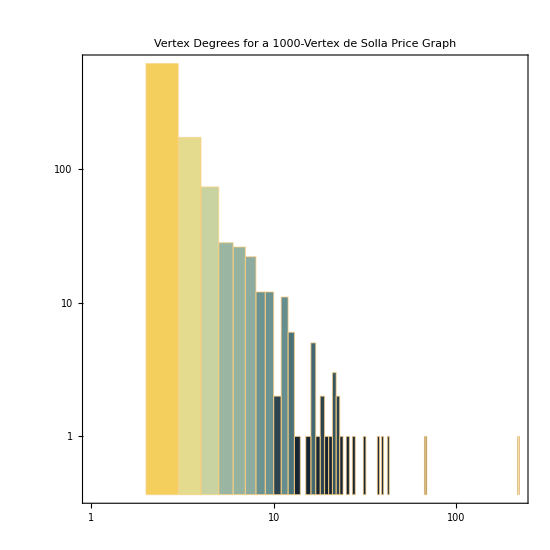

```mathematica
Histogram[data,ScalingFunctions->{"Log","Log"},Frame->True,ColorFunction->"StarryNightColors",AspectRatio->1,ImageSize->550,LabelStyle->Bold,PlotLabel->"Vertex Degrees for a 1000-Vertex de Solla Price Graph",BaseStyle->{FontFamily->"Helvetica"}]
```

Navarro-Frenkel-White profile for DM in galaxies.

```mathematica
https://en.wikipedia.org/wiki/Navarro%E2%80%93Frenk%E2%80%93White_profile
```

```mathematica
nfw = 1/(x(1+x)^2) (* where 1 is rho_o and x is r/R_scale *)
```

1/(x (1+x)^2)

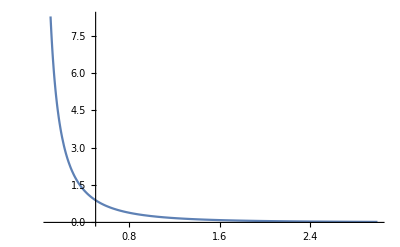

```mathematica
Plot[nfw,{x, 0.1, 3}, PlotRange->All]
```

The integrand in the mass integral.

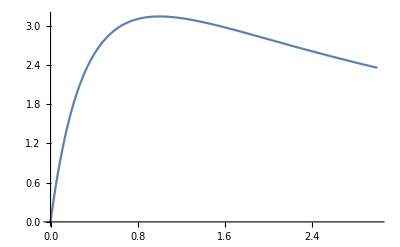

```mathematica
Plot[ 4π x^2 nfw, {x, 0, 3}, PlotRange->All]
```

```mathematica
$Assumptions=True;
mass=∫_0^r 4π x^2 nfw ⅆx
```

ConditionalExpression[4 π (-1+1/(1+r)+Log[1+r]),Re[r]>-1||r∉Reals]

```mathematica
mass= ∫_0^r 4π x^2 nfw ⅆx // Assuming[ r∈Reals && r>0,#]&
```

{ConditionalExpression[4 π (-1+1/(1+r)+Log[1+r]),Re[r]>-1||r∉Reals]}

```mathematica
Assuming[ r∈Reals && r>0, mass=∫_0^r 4π x^2 nfw ⅆx ]
```

4 π (-1+1/(1+r)+Log[1+r])

```mathematica
$Assumptions->Element[r,Reals]&&r>0;
mass=∫_0^r 4π x^2 nfw ⅆx //Assuming[Element[r,Reals] && r>0, #]
```

4 π (-1+1/(1+r)+Log[1+r])

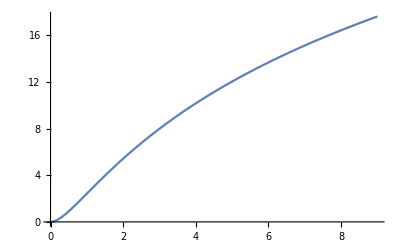

```mathematica
Plot[mass, {r, 0, 9}]
```

## Noise and Fourier space

The usual ensemble average over “many realizations of noise sources” can be replaced with the long time-average for “stationary, stochastic noise.”
Test this...

```mathematica
nn[t_,a_]:=(RandomReal[]-1/2)
```

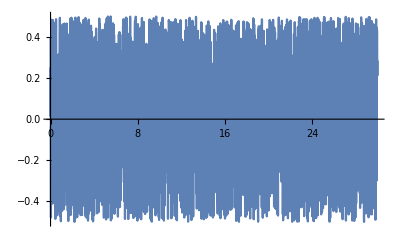

```mathematica
Plot[nn[t,0],{t,0,30}]
```

Discrete Fourier Transform is just that for  a list.

```mathematica
data=Table[nn[t,0],{i,1,5000}];
```

```mathematica
fdata =Fourier[data];
fdata[[1;;5]]
```

{0.0509564-5.0062×10^-18 ⅈ,0.213544-0.176033 ⅈ,-0.290007-0.388153 ⅈ,0.15449+0.171635 ⅈ,-0.103158+0.202531 ⅈ}

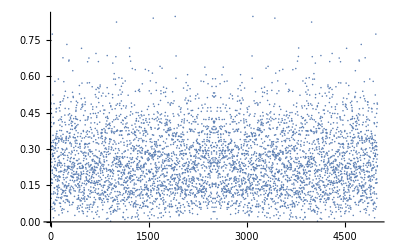

```mathematica
ListPlot[Abs[fdata]]
```

Check the relation ⟨n(f)n^*(f')⟩ = 1/2 δ(f-f') S_n(f) .  In Discrete Fourier transforms the freq is (index -1)/N, index-1 because Mathematica starts lists on 1.

```mathematica
fdata2 = Table[{(s-1)/Length[fdata],Abs[fdata[[s]] ]},{s,1,Length[fdata]}];
```

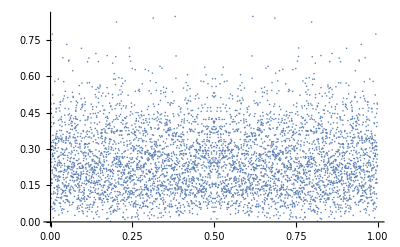
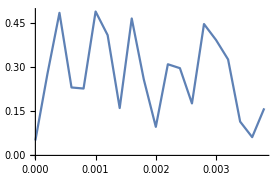

```mathematica
{ListPlot[fdata2 ],ListLinePlot[fdata2 [[1;;20]] ]}
```

{0.0509564-5.0062×10^-18 ⅈ,0.213544-0.176033 ⅈ,-0.290007-0.388153 ⅈ,0.15449+0.171635 ⅈ,-0.103158+0.202531 ⅈ,0.488987-0.00317849 ⅈ,-0.208678-0.351436 ⅈ,0.0844067-0.137121 ⅈ,-0.357097+0.298356 ⅈ,0.205619-0.156769 ⅈ}

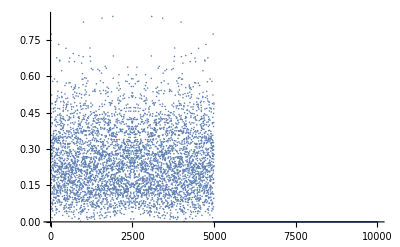

```mathematica
fdataPad = Table[If[i≤Length[fdata], fdata[[i]], 0.0],{i,1,2*Length[fdata]}];
fdataPad[[1;;10]]
ListPlot[Abs[fdataPad]] (* Pad the list with zeros. *)
```

```mathematica
fsqdata = Table[
Sum[ fdataPad[[i]]*Conjugate[fdataPad[[i+u-1]] ],{i,1,Length[fdata]} ],
{u, 1, Length[fdata]}
];
fsqdata[[1;;10]]
```

{412.407+0. ⅈ,-3.41831-1.66973 ⅈ,2.62233-4.13851 ⅈ,4.08853-1.7622 ⅈ,0.0567659-5.54748 ⅈ,-2.41817-5.99398 ⅈ,-4.39833+1.36098 ⅈ,0.329161+0.662316 ⅈ,0.129179-1.20226 ⅈ,-1.03738-7.38713 ⅈ}

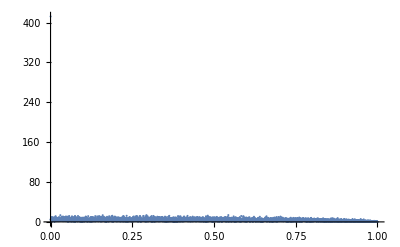

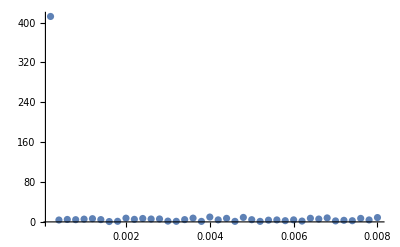

```mathematica
nsqdata = Transpose[ { Table[i/Length[fdata],{i,1,Length[fdata]}] ,Abs[fsqdata[[1;;Length[fdata]] ] ]  } ];
ListPlot[ nsqdata,
PlotRange->All]
ListPlot[ nsqdata[[1;;40]],
PlotRange->All]
```

```mathematica
num = Length[fdata]
Sqrt[ num(num-1)/2. ]
```

5000

3535.18

1.5 days and Two weeks of free-fall running to make Fig 1 in LPF paper.

```mathematica
{1/(1.5*24.*3600.),1/(14.*24.*3600.)}
```

{7.71605×10^-6,8.2672×10^-7}

26 windows of 40,000 secs (11.1 hours)

```mathematica
{1/40000.,40000./3600., 26*40000./3600./24.}
```

{0.000025,11.1111,12.037}

## Force from capacitance

Some capacitance numbers for the LISA Pathfinder (LPF).  Assume a 1 Volt measurement for capacitance, could be more but not much, could be less.

```mathematica
lcube = 0.046; (* meters *)
dgap = 3 10^-3; (* meters, 2.9 to 4mm *)
mass = 1.928; (* kg *)
lsep = 0.376; (* m *)
eps0 = 10^7/(4 π (3 10^8)^2); (* SI units, F/m *)
{capac = 4 π eps0 lcube^2/dgap,
efield = 1/(4 π eps0)1/lcube^2 ,(* V/m per Coulomb *)
ue = eps0 efield^2, (* F/m^2 per Coulomb squared *)
ueB = (1/(4 π))^2 1/eps0 ((capac volt)/lcube^2)^2(* F/m^2 for some voltage volt *)
}
```

{7.83704×10^-11,4.25331×10^12,1.59956×10^14,9.82438×10^-7 volt^2}

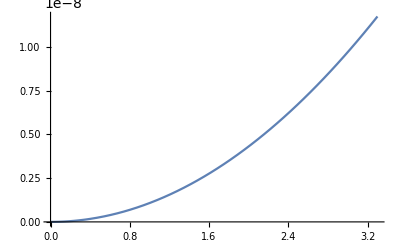

```mathematica
Plot[ueB*lcube^2/mass,{volt,0,3.3}]
```

```mathematica
avolt={0.5, 1.0, 2.0, 3.0, 3.3, 5.0};{{"volts","accel, m/s^2"}}~Join~Table[{avolt[[i]], ueB*lcube^2/mass/.volt->avolt[[i]]},{i,1,Length[avolt]}]//TableForm
```

volts | accel, m/s^2
0.5 | 2.69559×10^-10
1. | 1.07824×10^-9
2. | 4.31294×10^-9
3. | 9.70412×10^-9
3.3 | 1.1742×10^-8
5. | 2.69559×10^-8

```mathematica
??Sum
```

Sum[f,{i,i_max}] evaluates the sum ∑_(i=1)^i_max f. 
Sum[f,{i,i_min,i_max}] starts with i=i_min. 
Sum[f,{i,i_min,i_max,di}] uses steps di. 
Sum[f,{i,{i_1,i_2,…}}] uses successive values i_1, i_2, ….
Sum[f,{i,i_min,i_max},{j,j_min,j_max},…] evaluates the multiple sum ∑_(i=i_min)^i_max ∑_(j=j_min)^j_max …f. 
Sum[f,i] gives the indefinite sum ∑_i f.

Attributes[Sum]={HoldAll,Protected,ReadProtected}
 
Options[Sum]:={Assumptions:>$Assumptions,GenerateConditions→False,Method→Automatic,Regularization→None,VerifyConvergence→True}

```mathematica
abins = Table[i,{i,0,10}]
```

{0,1,2,3,4,5,6,7,8,9,10}

```mathematica
Length[abins]
```

11

```mathematica
Table[{i,Log10[i]//N},{i,1,10}]//TableForm
```

1 | 0.
2 | 0.30103
3 | 0.477121
4 | 0.60206
5 | 0.69897
6 | 0.778151
7 | 0.845098
8 | 0.90309
9 | 0.954243
10 | 1.

```mathematica
{Log[10.], E^2.30, E^2.31, Log10[E]//N, 10^0.43, E//N, Log[10.,2.], Log[2.,10.]}
```

{2.30259,9.97418,10.0744,0.434294,2.69153,2.71828,0.30103,3.32193}

```mathematica
adata={{1,2.3},{5,1.1},{3,2.0},{0,3.}};
```

```mathematica
Sort[adata]
```

{{0,3.},{1,2.3},{3,2.},{5,1.1}}

```mathematica
aaBins = {{1,2,3,4.5,6.4}};
aaData=Table[i*.333,{i,1,30}];
BinLists[aaData,aaBins]
```

{{1.332,1.665,1.998},{2.331,2.664,2.997},{3.33,3.663,3.996,4.329},{4.662,4.995,5.328,5.661,5.994,6.327}}

```mathematica
aaBins = {{1,2,3,4.5,6.4}};
aaData=Table[{i*.333,i*i/16.},{i,1,10}]
aBL=BinLists[aaData,aaBins,{{-Infinity, Infinity}}]
aBL[[1,1]]
aBL[[2,1]]
aBL[[3,1]]
aBL[[4,1]]
Length[aBL]
```

{{0.333,0.0625},{0.666,0.25},{0.999,0.5625},{1.332,1.},{1.665,1.5625},{1.998,2.25},{2.331,3.0625},{2.664,4.},{2.997,5.0625},{3.33,6.25}}

{{{{1.332,1.},{1.665,1.5625},{1.998,2.25}}},{{{2.331,3.0625},{2.664,4.},{2.997,5.0625}}},{{{3.33,6.25}}},{{}}}

{{1.332,1.},{1.665,1.5625},{1.998,2.25}}

{{2.331,3.0625},{2.664,4.},{2.997,5.0625}}

{{3.33,6.25}}

{}

4

```mathematica
Log[10.,E]
```

0.434294

```mathematica
0.43*0.058
```

0.02494

Join and Append?

```mathematica
aa={{1,2},{3,4.},{2.,2.3}};
bb={{10,11},{12,13},{14.,13.}};
(*aa~AppendTo~bb*)
```

```mathematica
cc=aa~Join~bb
aa=aa~Join~bb
```

{{1,2},{3,4.},{2.,2.3},{10,11},{12,13},{14.,13.}}

{{1,2},{3,4.},{2.,2.3},{10,11},{12,13},{14.,13.}}

```mathematica
aa
cc
```

{{1,2},{3,4.},{2.,2.3},{10,11},{12,13},{14.,13.}}

{{1,2},{3,4.},{2.,2.3},{10,11},{12,13},{14.,13.}}

```mathematica
√(1*1+2*2+3*3+4*4+5*5)//N[#,7]&
```

7.416198

```mathematica
aa={1,2,3,4,5.5}
5.0*aa
```

{1,2,3,4,5.5}

{5.,10.,15.,20.,27.5}

```mathematica
Sqrt[300.]
```

17.3205

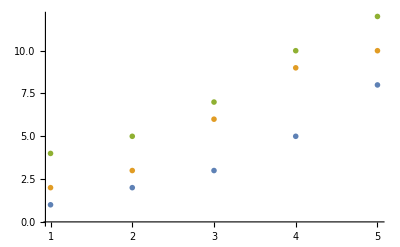

```mathematica
(* PlotMarkers   Graphics[{Blue,Circle[]}] "○"   *)ListPlot[{{1,2,3,5,8},{2,3,6,9,10},{4,5,7,10,12}},PlotMarkers->{-Graphics3D-,-Graphics3D-,-Graphics3D-},PlotRange->All,PlotRangeClipping->False]
```

```mathematica
Table[10^ii//N, {ii, -24, -16, 1}]
```

{1.×10^-24,1.×10^-23,1.×10^-22,1.×10^-21,1.×10^-20,1.×10^-19,1.×10^-18,1.×10^-17,1.×10^-16}

## Publication quality plots in Mathematica according to http://mathematica.stackexchange.com/questions/47711/preparing-2d-plots-for-publication

```mathematica
fx[x_]:=1/(Exp[-x-7]+1)+1/(Exp[x-7]+1)-1
```

```mathematica
(*blue=RGBColor[17.6/100,41.6/100,63.1/100];
u=Plot[fx[x],{x,-15,15},PlotRange->All,AxesLabel->{"x","fx(x)"},PlotStyle->Directive[AbsoluteThickness[0.5],blue]]*)
```

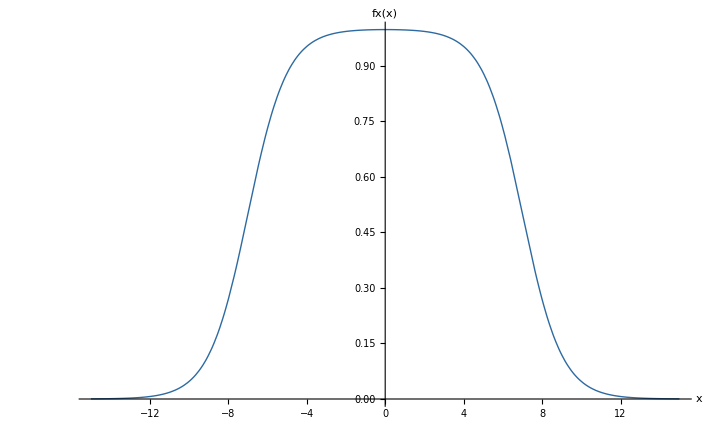

```mathematica
blue=RGBColor[17.6/100,41.6/100,63.1/100];
u=Plot[fx[x],{x,-15,15},PlotRange->All,AxesLabel->{"x","fx(x)"},PlotStyle->Directive[AbsoluteThickness[1],blue],
ImageSize->720]
```

```mathematica
(*Show[u,AxesStyle->Directive[AbsoluteThickness[0.5],6,FontFamily->"Helvetica"],ImageSize->120]
Export[FileNameJoin[{$UserDocumentsDirectory,"u1.pdf"}],%]   *)
```

```mathematica
Show[u,AxesStyle->Directive[AbsoluteThickness[1],18,FontFamily->"Helvetica"],ImageSize->720]
Export[FileNameJoin[{$UserDocumentsDirectory,"u1.pdf"}],%]  (* 18 pts on the font is good for a 10" Image, and the AbsoluteThickness is also in (printers) points. *)
```

-Graphics-

/home/gabella/Documents/u1.pdf

```mathematica
$UserDocumentsDirectory
```

/home/gabella/Documents